# Associahedron Net: K4

## Computed Data

```mathematica
Clear[facets];

facets={{{1,2,3,4},{1,2,6,1},{1,6,2,1},{1,6,1,2},{1,4,1,4}},{{1,2,3,4},{1,2,6,1},{2,1,6,1},{2,1,3,4}},{{1,2,3,4},{1,4,1,4},{3,2,1,4},{3,1,2,4},{2,1,3,4}},{{2,1,3,4},{2,1,6,1},{4,1,4,1},{4,1,2,3},{3,1,2,4}},{{3,1,2,4},{3,2,1,4},{4,2,1,3},{4,1,2,3}},{{4,1,2,3},{4,1,4,1},{4,3,2,1},{4,3,1,2},{4,2,1,3}},{{1,4,1,4},{1,6,1,2},{4,3,1,2},{4,2,1,3},{3,2,1,4}},{{1,6,1,2},{1,6,2,1},{4,3,2,1},{4,3,1,2}},{{1,2,6,1},{1,6,2,1},{4,3,2,1},{4,1,4,1},{2,1,6,1}}};
```

## Transform 4D → 3D

The facets lie on a 3D hyperplane. Each vertex has a component sum 10, so hyperplane is given by x+y+z+w==10, which can be rewritten as x+y+z+(w')==0 where w'==w-10. Then, a basis for this plane is

( 1 
 0 
 0 
 -1 ), ( 0 
 1 
 0 
 -1 ), ( 0 
 0 
 1 
 -1 ).

After an orthogonalizing algorithm, this basis becomes the left-most 3 columns of the matrix m1 below. For an input (x,y,z,w) vertex, reducing this matrix yields a point in R^3 that represents the original vertex in terms of this basis. This process transforms K4 on a 3D hyperplane embedded in 4D into a 3D polytope.

```mathematica
Clear[transform, facetsTransformed];

transform[{x_,y_,z_,w_}]:=Block[
{m1},
m1=RowReduce[({{1/Sqrt[2], -1/(√6), -1/(2 √3), x}, {0, √(2/3), -1/(2 √3), y}, {0, 0, (√3)/2, z}, {-1/Sqrt[2], -1/(√6), -1/(2 √3), w-10}})];
Return[{
m1[[1]][[4]],
m1[[2]][[4]],
m1[[3]][[4]]
}];
];

facetsTransformed=Table[Table[
transform[facets[[i]][[j]]],
{j,1,Length[facets[[i]]]}],
{i,1,Length[facets]}];
```

## Unfold Net 3D → 2D

`facetsTransformed` is an array of 2D faces. Each 2D face is an array of 3D points.

Idea: My goal is to take the each 2D face and flatten it’s points into the appropriate 2-dimensional shape. For a given face, this should be a matter of finding an orthonormal basis for the plane-2 that the face rests inside, and then expressing the vertices of the face in terms of that basis.

Problem: Does this actually yield a construction that fits together in 3D? I’ll have to print it out and check.

Idea: Each face is a 2D plane embedded in 3D space. After translating the face to the origin, it’s vertices should satisfy ax+by+cz==0 for some a,b,c∈R.

```mathematica
Clear[unfoldFacet,facetsUnfolded];

unfoldFacet[facet2_]:=Block[
{origin,b1,b2,facet2Linear,facet2Normal,unfoldVertex},

(*
 * Linearize facet2
 *)
origin=facet2[[1]]; (* choose arbitrary origin in plan *)
facet2Linear=Table[facet2[[i]]-origin,{i,1,Length[facet2]}]; (* translate to origin *)

(*
 * Constructing a basis for facet2
 *)
(* vector that is normal to the plane *)
facet2Normal=facet2Linear[[2]]×facet2Linear[[3]];
(* choose arbitrary vector to be first basis member *)
b1=Normalize[facet2Linear[[2]]];
(* second basis member is perpendicular to both facet2Normal and b1 *)
b2=Normalize[facet2Normal×b1];

(*Print[{b1,b2}];*)

(*
 * Convert vector3 to vector2
 *)
(* unfold vertex into 2D, in terms of basis *)
unfoldVertex[{x_,y_,z_}]:=Block[
{m},
m=RowReduce[({{b1[[1]], b2[[1]], x}, {b1[[2]], b2[[2]], y}, {b1[[3]], b2[[3]], z}})];
Return[{
m[[1]][[3]],
m[[2]][[3]]
}];
];

(* unfold all vertices *)
Return[Map[unfoldVertex,facet2Linear]];
];

facetsUnfolded=Map[unfoldFacet,facetsTransformed];
```

## Render Hull

```mathematica
Graphics3D[Map[Polygon,facetsTransformed]]
```

-Graphics3D-

## Render Net

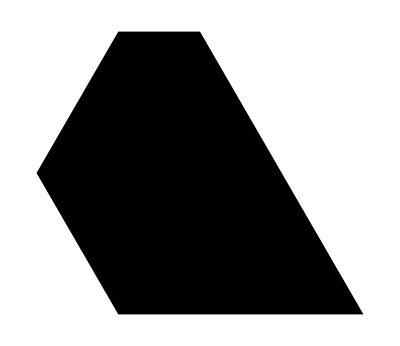
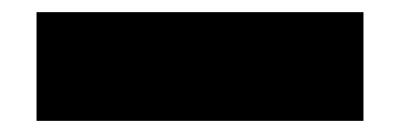
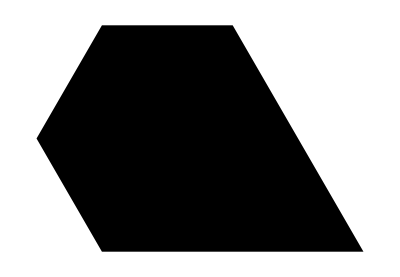
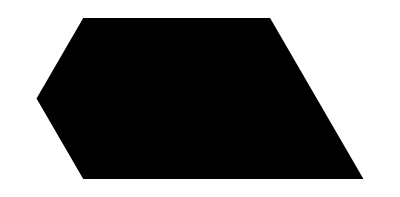

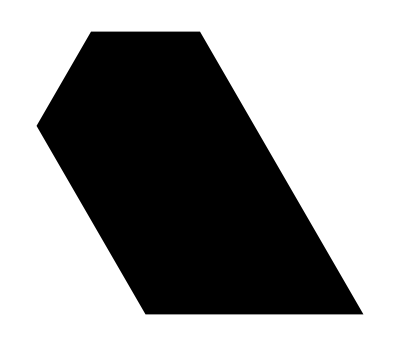
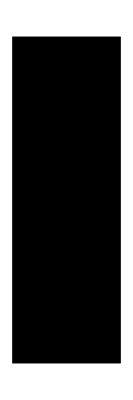
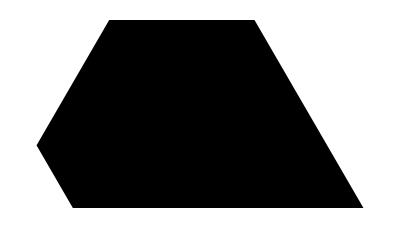
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Graphics[Polygon[facetsUnfolded[[i]]]],
{i,1,Length[facetsUnfolded]}]
```

## Testing

```mathematica
Clear[facet,b1,b2,basis];

facet=facetsTransformed[[1]];
b1=facet[[1]];
b2=facet[[2]];
basis=Orthogonalize[{b1,b2},Method->"Householder"];

facet[[1]]

basis[[1]]
basis[[2]]
```

{7/(√2),3 √(3/2),2 √3}

{7/10,(3 √3)/10,(√6)/5}

{-13/(10 √19),-31/(10 √57),(23 √(2/57))/5}